This code calculates the asymptotic values of the Wigner 9j-symbol as described in the publication: H. M. Haggard and R. G. Littlejohn, “Asymptotics of the Wigner 9j-symbol”, Classical and Quantum Gravity 27 (135010), 2010  
Copyright (C) 2012  Ilya Esterlis and Hal M. Haggard 

This program is free software : you can redistribute it and/or modify it under the terms of the GNU General Public License as published by the Free Software Foundation, either version 3 of the License, or (at your option) any later version. This program is distributed in the hope that it will be useful, but WITHOUT ANY WARRANTY; without even the implied warranty of
MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See the GNU General Public License for more details.You should have received a copy of the GNU General Public License along with this program. If not, see < http : // www.gnu.org/licenses/ > .

Questions about this code can be directed to: 
Ilya Esterlis, ilyae29 “add a symbol” gmail.com
or Hal Haggard, hhaggard “add a symbol” bard.edu

```mathematica
(*Finds the various dot products needed to reconstruct vectors J1,J2,J4,J5 and assembles them into a Gram matrix*)GramMatrix[j1_,j2_,j3_,j4_,j5_,j6_,j7_,j8_,j9_]:=Module[{J1dotJ2, J1dotJ4,J2dotJ5,J4dotJ5,J2dotJ4},{J1,J2,J3,J4,J5,J6,J7,J8,J9}={j1+1/2,j2+1/2,j3+1/2,j4+1/2,j5+1/2,j6+1/2,j7+1/2,j8+1/2,j9+1/2};
J1dotJ2=1/2((J3)^2-J1^2-J2^2);
J1dotJ4=1/2((J7)^2-J1^2-J4^2);
J2dotJ5=1/2((J8)^2-J2^2-J5^2);
J4dotJ5=1/2((J6)^2-J4^2-J5^2);
J2dotJ4=1/2 ((J9)^2-(J1)^2-(J2)^2-(J4)^2-(J5)^2)-(J1dotJ2+J1dotJ4+J1dotJ5+J2dotJ5+J4dotJ5);
({{J1^2, J1dotJ2, J1dotJ4, J1dotJ5}, {J1dotJ2, J2^2, J2dotJ4, J2dotJ5}, {J1dotJ4, J2dotJ4, J4^2, J4dotJ5}, {J1dotJ5, J2dotJ5, J4dotJ5, J5^2}})];
```

```mathematica
(*Given a Gram Matrix, GramReduce reconstructs the desired vectors*)
GramReduce[x1_]:=Module[{G=x1},
DiagonalVersion=Chop[(G;A=Orthogonalize[Eigenvectors[G]]; B=Transpose[A];A.G.B)];
SqrtReduced=√(Reduced=Delete[Delete[DiagonalVersion,4],{{1,4},{2,4},{3,4}}]);
Areduced=Delete[A,4];Breduced=Transpose[Areduced];
SqrtReduced.Areduced ]
```

```mathematica
(*Finds the nine vectors, corresponding to the first and second admissible roots*)VecFinder[j1_,j2_,j3_,j4_,j5_,j6_,j7_,j8_,j9_,I_]:=Module[
{J1,J2,J3,J4,J5,J6,J7,J8,J9,J},
G=GramMatrix[j1,j2,j3,j4,j5,j6,j7,j8,j9];
soln=Solve[Det[G]==0,J1dotJ5];
Geometries=J1dotJ5/.soln;
If[I==1,G=GramMatrix[j1,j2,j3,j4,j5,j6,j7,j8,j9]/.J1dotJ5->Geometries[[2]],
G=GramMatrix[j1,j2,j3,j4,j5,j6,j7,j8,j9]/.J1dotJ5->Geometries[[3]]];
M=GramReduce[G](*Columns are sought for vectors*);
J1=Extract[Transpose[M],1];
J2=Extract[Transpose[M],2];
J4=Extract[Transpose[M],3];
J5=Extract[Transpose[M],4];
J3=-(J1+J2);
J6=-(J4+J5);
J7=-(J1+J4);
J8=-(J2+J5);
J9=(J1+J2+J4+J5);
J={J1,J2,J3,J4,J5,J6,J7,J8,J9};
If[Det[{J1,J2,J4}]<0,J=-J];
J]
```

```mathematica
(*Finds dihedral angles, the last argument designates which root surface they are on*)
DihedralAngles[j1_,j2_,j3_,j4_,j5_,j6_,j7_,j8_,j9_,I_]:=Module[
{J1,J2,J3,J4,J5,J6,J7,J8,J9,Phi},
{J1,J2,J3,J4,J5,J6,J7,J8,J9}=VecFinder[j1,j2,j3,j4,j5,j6,j7,j8,j9,I];
CosTheta=Dot[Cross[#1,#2]/Norm[Cross[#1,#2]],Cross[#3,#4]/Norm[Cross[#3,#4]]]&;SinTheta=Dot[#1/Norm[#1],Cross[Cross[#1,#2]/Norm[Cross[#1,#2]],Cross[#3,#4]/Norm[Cross[#3,#4]]]]&;
COS={CosTheta[J1,J2,J1,J4],CosTheta[J1,J2,J2,J5],CosTheta[J1,J2,J3,J6],CosTheta[J4,J5,J1,J4],CosTheta[J4,J5,J2,J5],CosTheta[J4,J5,J6,J9],CosTheta[J7,J8,J1,J4],CosTheta[J7,J8,J2,J5],CosTheta[J9,J7,J9,J3]};
SIN={SinTheta[J1,J2,J1,J4],SinTheta[J2,J3,J2,J5],SinTheta[J3,J1,J3,J6],SinTheta[J4,J5,J4,J7],SinTheta[J5,J6,J5,J8],SinTheta[J6,J4,J6,J9],SinTheta[J7,J8,J7,J1],SinTheta[J8,J9,J8,J2],SinTheta[J9,J7,J9,J3]};
Phi=ConstantArray[0,9];
If[I==1,
For[i=1,i<10,i++,
Phi[[i]]=ArcTan[COS[[i]],SIN[[i]]]],
For[i=1,i<10,i++,
If[ArcTan[COS[[i]],SIN[[i]]]<0,Phi[[i]]=ArcTan[COS[[i]],SIN[[i]]]+2*Pi,Phi[[i]]=ArcTan[COS[[i]],SIN[[i]]]]
]
];
Phi]
```

```mathematica
(*Finds the Ampitude, last argument designates the root surface*)
DMatrix[j1_,j2_,j3_,j4_,j5_,j6_,j7_,j8_,j9_,I_]:=Module[
{J1,J2,J3,J4,J5,J6,J7,J8,J9},
{J1,J2,J3,J4,J5,J6,J7,J8,J9}=VecFinder[j1,j2,j3,j4,j5,j6,j7,j8,j9,I];
Det[{J1,J2,J4}]*Det[{J5,J4,J2}]-Det[{J2,J1,J5}]*Det[{J4,J5,J1}]]
```

```mathematica
(*Finds the Action, last argument designates the root surface*)
Action[j1_,j2_,j3_,j4_,j5_,j6_,j7_,j8_,j9_,I_]:=Module[{Phi,Jmag},
Jmag={j1+1/2,j2+1/2,j3+1/2,j4+1/2,j5+1/2,j6+1/2,j7+1/2,j8+1/2,j9+1/2};
Phi=DihedralAngles[j1,j2,j3,j4,j5,j6,j7,j8,j9,I];
Dot[Jmag,Phi]]
```

```mathematica
(*Computes the asymptotic 9j symbol*)
Approx9jsymbol[j1_,j2_,j3_,j4_,j5_,j6_,j7_,j8_,j9_]:=Module[
{A1,A2,S1,S2},
A1=1/(4*Pi*√Abs[DMatrix[j1,j2,j3,j4,j5,j6,j7,j8,j9,1]]);
A2=1/(4*Pi*√Abs[DMatrix[j1,j2,j3,j4,j5,j6,j7,j8,j9,2]]);
S1=Action[j1,j2,j3,j4,j5,j6,j7,j8,j9,1];
S2=Action[j1,j2,j3,j4,j5,j6,j7,j8,j9,2];
A1*Cos[S1]+A2*Sin[S2]]
```

```mathematica
(*Enter angular momentum values here*)
{{{j1, j2, j3}, {j4, j5, j6}, {j7, j8, j9}}}={{{129/2., 137/2., j3}, {113/2., 121/2., 50.}, {64., 108., 90.}}};
```

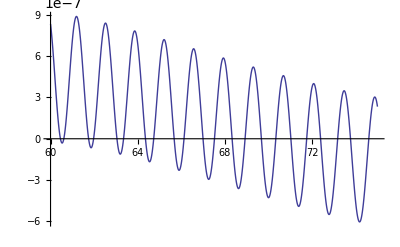

```mathematica
Plot[Approx9jsymbol[j1,j2,j3,j4,j5,j6,j7,j8,j9],{j3,60,75}]
```

```mathematica
(*Computes the exact 9j symbol at allowed values*)
NineJSymbol=
 Sum[(-1)^(2*k)*(2*k+1)*
SixJSymbol[{#1,#9,k},{#8,#4,#7}]*
SixJSymbol[{#8,#4,k},{#6,#2,#5}]*
SixJSymbol[{#6,#2,k},{#1,#9,#3}],
{k,Max[Abs[#1-#9],Abs[#8-#4],Abs[#6-#2]],Min[#1+#9,#8+#4,#6+#2]}]&;
```

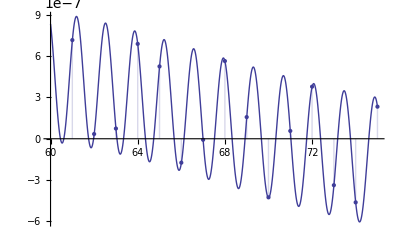

```mathematica
(*Comparison of the exact (sticks) and asymptotic (curve) values of the 9j-symbol*)
L=ConstantArray[0,15];For[i=1,i<16,i++,L[[i]]={60+i,NineJSymbol[j1,j2,60+i,j4,j5,j6,j7,j8,j9]}]
```